```mathematica
b1=basis[[1]]
b2=basis[[2]]
c=Table[<|{2*(i+1),j+1}->
{FaceForm[GrayLevel[1-Reverse[initialConditions2D,1][[j+1]][[2(i+1)]]]],EdgeForm[Black],Triangle[{(i+1)*b1+j*b2,i*b1+(j+1)*b2,(i+1)*b1+(j+1)*b2}]}|>
,{i,0,5-1},{j,0,3-1}]
```

{1,0}

{0.5,(√3)/2}

{{<|{2,1}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{1.,0},{0.5,(√3)/2},{1.5,(√3)/2}}]}|>,<|{2,2}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{1.5,(√3)/2},{1.,√3},{2.,√3}}]}|>,<|{2,3}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{2.,√3},{1.5,(3 √3)/2},{2.5,(3 √3)/2}}]}|>},{<|{4,1}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{2.,0},{1.5,(√3)/2},{2.5,(√3)/2}}]}|>,<|{4,2}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{2.5,(√3)/2},{2.,√3},{3.,√3}}]}|>,<|{4,3}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{3.,√3},{2.5,(3 √3)/2},{3.5,(3 √3)/2}}]}|>},{<|{6,1}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{3.,0},{2.5,(√3)/2},{3.5,(√3)/2}}]}|>,<|{6,2}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{3.5,(√3)/2},{3.,√3},{4.,√3}}]}|>,<|{6,3}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{4.,√3},{3.5,(3 √3)/2},{4.5,(3 √3)/2}}]}|>},{<|{8,1}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{4.,0},{3.5,(√3)/2},{4.5,(√3)/2}}]}|>,<|{8,2}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{4.5,(√3)/2},{4.,√3},{5.,√3}}]}|>,<|{8,3}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{5.,√3},{4.5,(3 √3)/2},{5.5,(3 √3)/2}}]}|>},{<|{10,1}→{FaceForm[GrayLevel[0]],EdgeForm[GrayLevel[0]],Triangle[{{5.,0},{4.5,(√3)/2},{5.5,(√3)/2}}]}|>,<|{10,2}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{5.5,(√3)/2},{5.,√3},{6.,√3}}]}|>,<|{10,3}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{6.,√3},{5.5,(3 √3)/2},{6.5,(3 √3)/2}}]}|>}}

```mathematica
Flatten[c][[1]]
```

<|{2,1}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{1.,0},{0.5,(√3)/2},{1.5,(√3)/2}}]}|>

```mathematica
d=<||>;
Do[AppendTo[d,Flatten[c][[i]]],{i,1,Times[Dimensions[c][[1]],Dimensions[c][[2]]]}]
```

```mathematica
d
```

<|{2,1}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{1.,0},{0.5,(√3)/2},{1.5,(√3)/2}}]},{2,2}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{1.5,(√3)/2},{1.,√3},{2.,√3}}]},{2,3}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{2.,√3},{1.5,(3 √3)/2},{2.5,(3 √3)/2}}]},{4,1}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{2.,0},{1.5,(√3)/2},{2.5,(√3)/2}}]},{4,2}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{2.5,(√3)/2},{2.,√3},{3.,√3}}]},{4,3}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{3.,√3},{2.5,(3 √3)/2},{3.5,(3 √3)/2}}]},{6,1}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{3.,0},{2.5,(√3)/2},{3.5,(√3)/2}}]},{6,2}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{3.5,(√3)/2},{3.,√3},{4.,√3}}]},{6,3}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{4.,√3},{3.5,(3 √3)/2},{4.5,(3 √3)/2}}]},{8,1}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{4.,0},{3.5,(√3)/2},{4.5,(√3)/2}}]},{8,2}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{4.5,(√3)/2},{4.,√3},{5.,√3}}]},{8,3}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{5.,√3},{4.5,(3 √3)/2},{5.5,(3 √3)/2}}]},{10,1}→{FaceForm[GrayLevel[0]],EdgeForm[GrayLevel[0]],Triangle[{{5.,0},{4.5,(√3)/2},{5.5,(√3)/2}}]},{10,2}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{5.5,(√3)/2},{5.,√3},{6.,√3}}]},{10,3}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{6.,√3},{5.5,(3 √3)/2},{6.5,(3 √3)/2}}]}|>

```mathematica
Lookup[d,{{2,1}}]
```

{{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{1.,0},{0.5,(√3)/2},{1.5,(√3)/2}}]}}

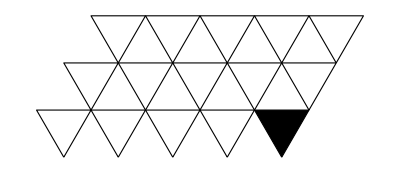

```mathematica
Graphics[Table[Lookup[d,{{2i,j}}],{i,1,Dimensions[c][[1]]},{j,1,Dimensions[c][[2]]}]]
```

```mathematica
oddTriangleCellsAssoc[basis_,state_,c_:{},d_:<||>]:=Module[{b1=basis[[1]],b2=basis[[2]],d1=Dimensions[state][[1]],
d2=If[EvenQ[Dimensions[state][[2]]],(Dimensions[state][[2]])/2,(Dimensions[state][[2]]+1)/2],flipped=Reverse[state,1]},
c=Table[<|{2*i+1,j+1}->
{FaceForm[GrayLevel[1-flipped[[j+1]][[2i+1]]]],EdgeForm[Black],Triangle[{i*b1+j*b2,(i+1)*b1+j*b2,i*b1+(j+1)*b2}]}|>
,{i,0,d2-1},{j,0,d1-1}];
Do[AppendTo[d,Flatten[c][[i]]],{i,1,d1*d2}]
];
```

```mathematica
temph=oddTriangleCellsAssoc[basis,initialConditions2D]
```

```mathematica
d
```

{{{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{0.,0},{1.,0},{0.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{0.5,(√3)/2},{1.5,(√3)/2},{1.,√3}}]},{FaceForm[GrayLevel[0]],EdgeForm[GrayLevel[0]],Triangle[{{1.,√3},{2.,√3},{1.5,(3 √3)/2}}]}},{{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{1.,0},{2.,0},{1.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{1.5,(√3)/2},{2.5,(√3)/2},{2.,√3}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{2.,√3},{3.,√3},{2.5,(3 √3)/2}}]}},{{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{2.,0},{3.,0},{2.5,(√3)/2}}]},{FaceForm[GrayLevel[0]],EdgeForm[GrayLevel[0]],Triangle[{{2.5,(√3)/2},{3.5,(√3)/2},{3.,√3}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{3.,√3},{4.,√3},{3.5,(3 √3)/2}}]}},{{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{3.,0},{4.,0},{3.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{3.5,(√3)/2},{4.5,(√3)/2},{4.,√3}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{4.,√3},{5.,√3},{4.5,(3 √3)/2}}]}},{{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{4.,0},{5.,0},{4.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{4.5,(√3)/2},{5.5,(√3)/2},{5.,√3}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{5.,√3},{6.,√3},{5.5,(3 √3)/2}}]}},{{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{5.,0},{6.,0},{5.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{5.5,(√3)/2},{6.5,(√3)/2},{6.,√3}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{6.,√3},{7.,√3},{6.5,(3 √3)/2}}]}}}

```mathematica
Flatten[c][[1]]
```

<|{2,1}→{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{1.,0},{0.5,(√3)/2},{1.5,(√3)/2}}]}|>